```mathematica
ClearAll["Global`*"] (*clear all variables to avoid errors*)
NotebookSave[]
Drop[DateList[],{1,3}](*Hour when the computation started*)
Get["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Functions\\Function.m"]; (*get function "Simul" written on file Function.nb. This function does exactly the same as the whole file Simulation.nb, only it does it as a single function with a single return that corresponds to the option price.*)
(*This function expects the inputs - Simul[M,callput,n,T,K,r,sigma,S0] (see below)*)
```

{16,29,30.3454435}

Distribution Parameters

```mathematica
(*we assume the variables for the interest rate (r), stock price volatility (σ) and initial stock price (S0) follow a normal distribution. This particular choice of variables was arbitrary.*)
(*The final output of the sensitivity analysis, Vi, for each of these variables, will indicate what fraction of price variance is generated by the individual variance of the respective input.*)
rm=0.06; (*interest rate expected value*)
rs=0.01; (*interest rate standard deviation*)
sigmam=0.2; (*stock price volatility expected value*)
sigmas=0.005;(*stock price volatility standard deviation*)
S0m=45.; (*initial stock price expected value*)
S0s=0.28284;(*initial stock price standard deviation*)
```

Set Parameters

```mathematica
Num=1500; (*Number of simulations per vector - See the article by Sobol for more information*)
M=50000; (*Number of paths to be generated on each simulation*)
callput="Put"; (*Type of option - "Call" or "Put"*)
n=48.; (*Number of exercise chances per year*)
T=0.375; (*Number of years until exercise*)
k=40.; (*Strike price*)
Exporting=True;
ExportingExtention=12; (*Choose True if you want the final matrices and images to be exported. Choose False otherwise. If you want to export the results, change the paths at the end of the file to the appropriate destination.*)

(*It should be noted that a total number of "Num*(number of random input variabes + 2)", or, in this case, Num*5 instances of the simulation will have to be performed. This means that a large value of Num will result in a very long computation time*)
```

Sensitivity Analysis

```mathematica
distrib={rdist,sigmadist,S0dist}={NormalDistribution[rm,rs],NormalDistribution[sigmam,sigmas],NormalDistribution[S0m,S0s]};(*Vector with the distributions of each input variable.*)
```

```mathematica
matrix=Table[distrib,{i,1,Num}];(*Table with distributions*)
```

```mathematica
MatRand1=Map[RandomVariate,matrix,{2}];(*Matrix with the randomized inputs to be used on vector A.*)
MatRand2=Map[RandomVariate,matrix,{2}];(*Matrix with the randomized inputs to be used on vector B*)
```

```mathematica
Param=Table[{M,callput,n,T,k},{i,1,Num}];(*Matrix with non-random input parameters*)
```

```mathematica
MatA=Join[Param,MatRand1,2];(*Matrix with input parameters (non-random + random) to be used on vector A. Each row contains the set of parameters needed to obtain the option price.*)
MatB=Join[Param,MatRand2,2];(*Matrix with input parameters (non-random + random) to be used on vector B*)
```

```mathematica
For[i=Dimensions[Param][[2]]+1;VMat={},i≤Dimensions[MatA][[2]],i++,tmp=MatB;tmp[[All,i]]=MatA[[All,i]];AppendTo[VMat,tmp]] (*Generation of input parameter matrices VMat[[i]]. They are similar to matrix MatB, with the i^th column replaced by the i^th column of matrix MatA*)
```

```mathematica
fA=ParallelTable[Simul@@MatA[[it3]],{it3,1,Num}];//AbsoluteTiming(*Vector A generation. We use the input matrix MatA and calculate the option price using all the input parameters on each row*)
```

{6451.07,Null}

```mathematica
fB=ParallelTable[Simul@@MatB[[it4]],{it4,1,Num}];(*Vector B generation.*)
```

```mathematica
Monitor[For[it2=1;fVA={},it2<=Dimensions[VMat][[1]],it2++,tmp=ParallelTable[Simul@@VMat[[it2,it1]],{it1,1,Num}];AppendTo[fVA,tmp]],ProgressIndicator[it2,{1,Dimensions[VMat][[1]]}]];(*Vectors fVA[[i]] generation. The inputs used were the matrices VMat[[i]].*)
```

```mathematica
For[x=1;Vi={},x≤Dimensions[fVA][[1]],x++,tmp=1/Num*Sum[fA[[w]]*(fVA[[x,w]]-fB[[w]]),{w,1,Num}];AppendTo[Vi,tmp]] ;Vi(*Contribution of each variable to the final variance. The output is (r,sigma,S0).*)
```

{0.0000319916,0.000814163,0.00149952}

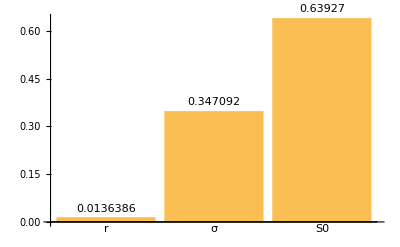

```mathematica
BarChart[Vi/Total[Vi,2],ChartLabels->{"r","σ","S0"},LabelingFunction->Above]
```

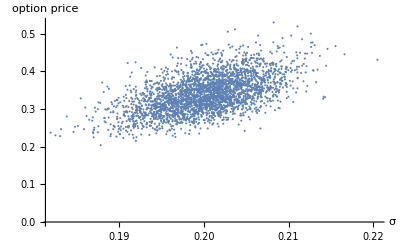

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}]
```

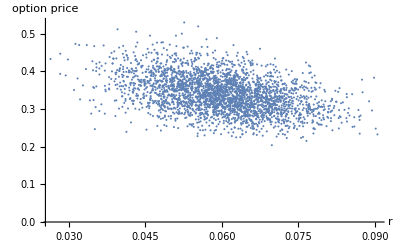

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]
```

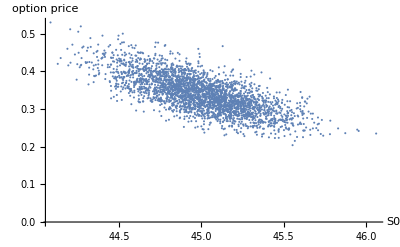

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}]
```

```mathematica
(*If the variable Exporting was set to True, export the results. This might be useful to avoid repeating lengthy computations.*)
If[Exporting,Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatA"<>ToString[ExportingExtention]<>".m",MatA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatB"<>ToString[ExportingExtention]<>".m",MatB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fA"<>ToString[ExportingExtention]<>".m",fA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fB"<>ToString[ExportingExtention]<>".m",fB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fVA"<>ToString[ExportingExtention]<>".m",fVA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\Param"<>ToString[ExportingExtention]<>".m",Param[[1]]],];
If[Exporting,Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\sigma"<>ToString[ExportingExtention]<>".eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}],"eps"];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\r"<>ToString[ExportingExtention]<>".eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\S0"<>ToString[ExportingExtention]<>".eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}],"eps"],];
```

```mathematica
NotebookSave[]
```

```mathematica
Vars={{0.125,{7.393768280637135*10^(-6),0.00004322870002285361,0.0001161124225516977}},{0.25,{0.00009111790302489225,0.00028003776005258534,0.000692573548432537}},{0.5,{0.0005231448921959867,0.0015428161724180445,0.002867963486243189}},{0.75,{0.001987249189636324,0.0033591847909178133,0.004403610823836773}},{1.0,{0.0022458332820427464,0.0036861312258917676,0.002725724722454316}}};
```

```mathematica
ClearAll["Global`*"] (*clear all variables to avoid errors*)
NotebookSave[]
Drop[DateList[],{1,3}](*Hour when the computation started*)
Get["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Functions\\Function.m"]; (*get function "Simul" written on file Function.nb. This function does exactly the same as the whole file Simulation.nb, only it does it as a single function with a single return that corresponds to the option price.*)
(*This function expects the inputs - Simul[M,callput,n,T,K,r,sigma,S0] (see below)*)
```

{1,23,40.0829939}

Distribution Parameters

```mathematica
(*we assume the variables for the interest rate (r), stock price volatility (σ) and initial stock price (S0) follow a normal distribution. This particular choice of variables was arbitrary.*)
(*The final output of the sensitivity analysis, Vi, for each of these variables, will indicate what fraction of price variance is generated by the individual variance of the respective input.*)
rm=0.06; (*interest rate expected value*)
rs=0.01; (*interest rate standard deviation*)
sigmam=0.2; (*stock price volatility expected value*)
sigmas=0.005;(*stock price volatility standard deviation*)
S0m=45.; (*initial stock price expected value*)
S0s=0.28284;(*initial stock price standard deviation*)
```

Set Parameters

```mathematica
Num=1500; (*Number of simulations per vector - See the article by Sobol for more information*)
M=50000; (*Number of paths to be generated on each simulation*)
callput="Put"; (*Type of option - "Call" or "Put"*)
n=48.; (*Number of exercise chances per year*)
T=0.625; (*Number of years until exercise*)
k=40.; (*Strike price*)
Exporting=True;
ExportingExtention=13; (*Choose True if you want the final matrices and images to be exported. Choose False otherwise. If you want to export the results, change the paths at the end of the file to the appropriate destination.*)

(*It should be noted that a total number of "Num*(number of random input variabes + 2)", or, in this case, Num*5 instances of the simulation will have to be performed. This means that a large value of Num will result in a very long computation time*)
```

Sensitivity Analysis

```mathematica
distrib={rdist,sigmadist,S0dist}={NormalDistribution[rm,rs],NormalDistribution[sigmam,sigmas],NormalDistribution[S0m,S0s]};(*Vector with the distributions of each input variable.*)
```

```mathematica
matrix=Table[distrib,{i,1,Num}];(*Table with distributions*)
```

```mathematica
MatRand1=Map[RandomVariate,matrix,{2}];(*Matrix with the randomized inputs to be used on vector A.*)
MatRand2=Map[RandomVariate,matrix,{2}];(*Matrix with the randomized inputs to be used on vector B*)
```

```mathematica
Param=Table[{M,callput,n,T,k},{i,1,Num}];(*Matrix with non-random input parameters*)
```

```mathematica
MatA=Join[Param,MatRand1,2];(*Matrix with input parameters (non-random + random) to be used on vector A. Each row contains the set of parameters needed to obtain the option price.*)
MatB=Join[Param,MatRand2,2];(*Matrix with input parameters (non-random + random) to be used on vector B*)
```

```mathematica
For[i=Dimensions[Param][[2]]+1;VMat={},i≤Dimensions[MatA][[2]],i++,tmp=MatB;tmp[[All,i]]=MatA[[All,i]];AppendTo[VMat,tmp]] (*Generation of input parameter matrices VMat[[i]]. They are similar to matrix MatB, with the i^th column replaced by the i^th column of matrix MatA*)
```

```mathematica
fA=ParallelTable[Simul@@MatA[[it3]],{it3,1,Num}];//AbsoluteTiming(*Vector A generation. We use the input matrix MatA and calculate the option price using all the input parameters on each row*)
```

{15053.6,Null}

```mathematica
fB=ParallelTable[Simul@@MatB[[it4]],{it4,1,Num}];(*Vector B generation.*)
```

```mathematica
Monitor[For[it2=1;fVA={},it2<=Dimensions[VMat][[1]],it2++,tmp=ParallelTable[Simul@@VMat[[it2,it1]],{it1,1,Num}];AppendTo[fVA,tmp]],ProgressIndicator[it2,{1,Dimensions[VMat][[1]]}]];(*Vectors fVA[[i]] generation. The inputs used were the matrices VMat[[i]].*)
```

```mathematica
For[x=1;Vi={},x≤Dimensions[fVA][[1]],x++,tmp=1/Num*Sum[fA[[w]]*(fVA[[x,w]]-fB[[w]]),{w,1,Num}];AppendTo[Vi,tmp]] ;Vi(*Contribution of each variable to the final variance. The output is (r,sigma,S0).*)
```

{0.00238335,0.00109489,0.00205214}

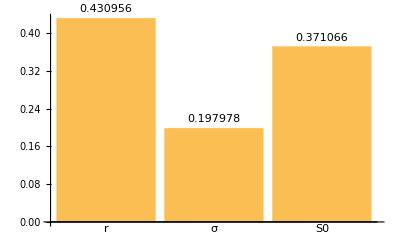

```mathematica
BarChart[Vi/Total[Vi,2],ChartLabels->{"r","σ","S0"},LabelingFunction->Above]
```

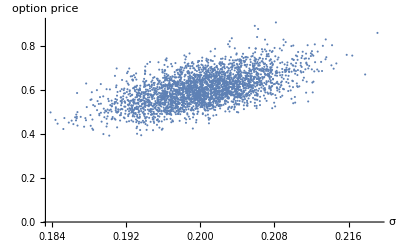

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}]
```

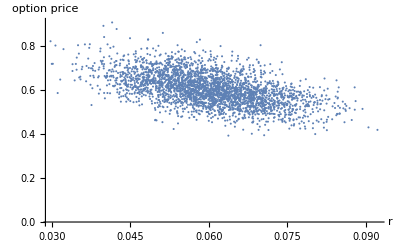

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]
```

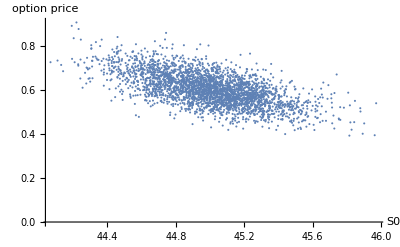

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}]
```

```mathematica
(*If the variable Exporting was set to True, export the results. This might be useful to avoid repeating lengthy computations.*)
If[Exporting,Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatA"<>ToString[ExportingExtention]<>".m",MatA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatB"<>ToString[ExportingExtention]<>".m",MatB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fA"<>ToString[ExportingExtention]<>".m",fA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fB"<>ToString[ExportingExtention]<>".m",fB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fVA"<>ToString[ExportingExtention]<>".m",fVA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\Param"<>ToString[ExportingExtention]<>".m",Param[[1]]],];
If[Exporting,Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\sigma"<>ToString[ExportingExtention]<>".eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}],"eps"];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\r"<>ToString[ExportingExtention]<>".eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\S0"<>ToString[ExportingExtention]<>".eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}],"eps"],];
```

```mathematica
NotebookSave[]
```

```mathematica
Vars={{0.125,{7.393768280637135*10^(-6),0.00004322870002285361,0.0001161124225516977}},{0.25,{0.00009111790302489225,0.00028003776005258534,0.000692573548432537}},{0.5,{0.0005231448921959867,0.0015428161724180445,0.002867963486243189}},{0.75,{0.001987249189636324,0.0033591847909178133,0.004403610823836773}},{1.0,{0.0022458332820427464,0.0036861312258917676,0.002725724722454316}}};
```

```mathematica
ClearAll["Global`*"] (*clear all variables to avoid errors*)
NotebookSave[]
Drop[DateList[],{1,3}](*Hour when the computation started*)
Get["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Functions\\Function.m"]; (*get function "Simul" written on file Function.nb. This function does exactly the same as the whole file Simulation.nb, only it does it as a single function with a single return that corresponds to the option price.*)
(*This function expects the inputs - Simul[M,callput,n,T,K,r,sigma,S0] (see below)*)
```

{22,23,31.5158437}

Distribution Parameters

```mathematica
(*we assume the variables for the interest rate (r), stock price volatility (σ) and initial stock price (S0) follow a normal distribution. This particular choice of variables was arbitrary.*)
(*The final output of the sensitivity analysis, Vi, for each of these variables, will indicate what fraction of price variance is generated by the individual variance of the respective input.*)
rm=0.06; (*interest rate expected value*)
rs=0.01; (*interest rate standard deviation*)
sigmam=0.2; (*stock price volatility expected value*)
sigmas=0.005;(*stock price volatility standard deviation*)
S0m=45.; (*initial stock price expected value*)
S0s=0.28284;(*initial stock price standard deviation*)
```

Set Parameters

```mathematica
Num=1500; (*Number of simulations per vector - See the article by Sobol for more information*)
M=50000; (*Number of paths to be generated on each simulation*)
callput="Put"; (*Type of option - "Call" or "Put"*)
n=48.; (*Number of exercise chances per year*)
T=0.875; (*Number of years until exercise*)
k=40.; (*Strike price*)
Exporting=True;
ExportingExtention=14; (*Choose True if you want the final matrices and images to be exported. Choose False otherwise. If you want to export the results, change the paths at the end of the file to the appropriate destination.*)

(*It should be noted that a total number of "Num*(number of random input variabes + 2)", or, in this case, Num*5 instances of the simulation will have to be performed. This means that a large value of Num will result in a very long computation time*)
```

Sensitivity Analysis

```mathematica
distrib={rdist,sigmadist,S0dist}={NormalDistribution[rm,rs],NormalDistribution[sigmam,sigmas],NormalDistribution[S0m,S0s]};(*Vector with the distributions of each input variable.*)
```

```mathematica
matrix=Table[distrib,{i,1,Num}];(*Table with distributions*)
```

```mathematica
MatRand1=Map[RandomVariate,matrix,{2}];(*Matrix with the randomized inputs to be used on vector A.*)
MatRand2=Map[RandomVariate,matrix,{2}];(*Matrix with the randomized inputs to be used on vector B*)
```

```mathematica
Param=Table[{M,callput,n,T,k},{i,1,Num}];(*Matrix with non-random input parameters*)
```

```mathematica
MatA=Join[Param,MatRand1,2];(*Matrix with input parameters (non-random + random) to be used on vector A. Each row contains the set of parameters needed to obtain the option price.*)
MatB=Join[Param,MatRand2,2];(*Matrix with input parameters (non-random + random) to be used on vector B*)
```

```mathematica
For[i=Dimensions[Param][[2]]+1;VMat={},i≤Dimensions[MatA][[2]],i++,tmp=MatB;tmp[[All,i]]=MatA[[All,i]];AppendTo[VMat,tmp]] (*Generation of input parameter matrices VMat[[i]]. They are similar to matrix MatB, with the i^th column replaced by the i^th column of matrix MatA*)
```

```mathematica
fA=ParallelTable[Simul@@MatA[[it3]],{it3,1,Num}];//AbsoluteTiming(*Vector A generation. We use the input matrix MatA and calculate the option price using all the input parameters on each row*)
```

{27084.1,Null}

```mathematica
fB=ParallelTable[Simul@@MatB[[it4]],{it4,1,Num}];(*Vector B generation.*)
```

```mathematica
Monitor[For[it2=1;fVA={},it2<=Dimensions[VMat][[1]],it2++,tmp=ParallelTable[Simul@@VMat[[it2,it1]],{it1,1,Num}];AppendTo[fVA,tmp]],ProgressIndicator[it2,{1,Dimensions[VMat][[1]]}]];(*Vectors fVA[[i]] generation. The inputs used were the matrices VMat[[i]].*)
```

```mathematica
For[x=1;Vi={},x≤Dimensions[fVA][[1]],x++,tmp=1/Num*Sum[fA[[w]]*(fVA[[x,w]]-fB[[w]]),{w,1,Num}];AppendTo[Vi,tmp]] ;Vi(*Contribution of each variable to the final variance. The output is (r,sigma,S0).*)
```

{0.00260908,0.00117216,0.00414671}

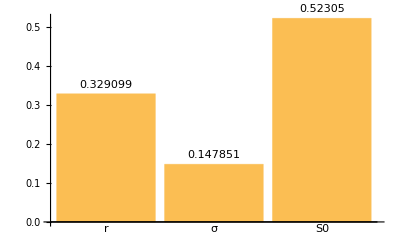

```mathematica
BarChart[Vi/Total[Vi,2],ChartLabels->{"r","σ","S0"},LabelingFunction->Above]
```

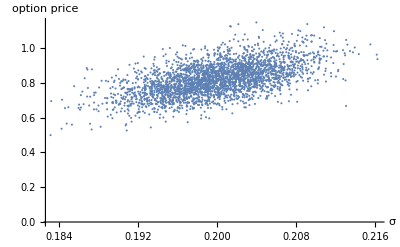

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}]
```

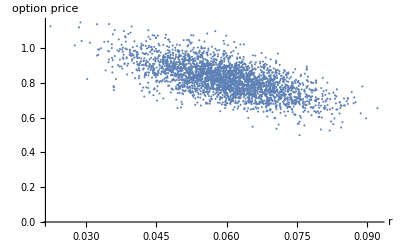

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]
```

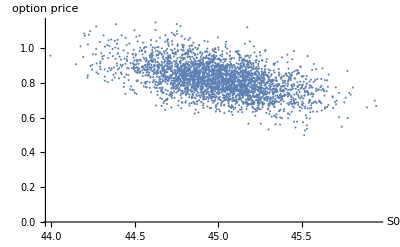

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}]
```

```mathematica
(*If the variable Exporting was set to True, export the results. This might be useful to avoid repeating lengthy computations.*)
If[Exporting,Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatA"<>ToString[ExportingExtention]<>".m",MatA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatB"<>ToString[ExportingExtention]<>".m",MatB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fA"<>ToString[ExportingExtention]<>".m",fA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fB"<>ToString[ExportingExtention]<>".m",fB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fVA"<>ToString[ExportingExtention]<>".m",fVA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\Param"<>ToString[ExportingExtention]<>".m",Param[[1]]],];
If[Exporting,Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\sigma"<>ToString[ExportingExtention]<>".eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}],"eps"];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\r"<>ToString[ExportingExtention]<>".eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\S0"<>ToString[ExportingExtention]<>".eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}],"eps"],];
```

```mathematica
NotebookSave[]
```

```mathematica
Vars={{0.125,{7.393768280637135*10^(-6),0.00004322870002285361,0.0001161124225516977}},{0.25,{0.00009111790302489225,0.00028003776005258534,0.000692573548432537}},{0.5,{0.0005231448921959867,0.0015428161724180445,0.002867963486243189}},{0.75,{0.001987249189636324,0.0033591847909178133,0.004403610823836773}},{1.0,{0.0022458332820427464,0.0036861312258917676,0.002725724722454316}}};
```

```mathematica
ClearAll["Global`*"] (*clear all variables to avoid errors*)
NotebookSave[]
Drop[DateList[],{1,3}](*Hour when the computation started*)
Get["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Functions\\Function.m"]; (*get function "Simul" written on file Function.nb. This function does exactly the same as the whole file Simulation.nb, only it does it as a single function with a single return that corresponds to the option price.*)
(*This function expects the inputs - Simul[M,callput,n,T,K,r,sigma,S0] (see below)*)
```

{12,26,8.7392712}

Distribution Parameters

```mathematica
(*we assume the variables for the interest rate (r), stock price volatility (σ) and initial stock price (S0) follow a normal distribution. This particular choice of variables was arbitrary.*)
(*The final output of the sensitivity analysis, Vi, for each of these variables, will indicate what fraction of price variance is generated by the individual variance of the respective input.*)
rm=0.06; (*interest rate expected value*)
rs=0.01; (*interest rate standard deviation*)
sigmam=0.2; (*stock price volatility expected value*)
sigmas=0.005;(*stock price volatility standard deviation*)
S0m=45.; (*initial stock price expected value*)
S0s=0.28284;(*initial stock price standard deviation*)
```

Set Parameters

```mathematica
Num=1500; (*Number of simulations per vector - See the article by Sobol for more information*)
M=50000; (*Number of paths to be generated on each simulation*)
callput="Put"; (*Type of option - "Call" or "Put"*)
n=48.; (*Number of exercise chances per year*)
T=0.625; (*Number of years until exercise*)
k=40.; (*Strike price*)
Exporting=True;
ExportingExtention=13; (*Choose True if you want the final matrices and images to be exported. Choose False otherwise. If you want to export the results, change the paths at the end of the file to the appropriate destination.*)

(*It should be noted that a total number of "Num*(number of random input variabes + 2)", or, in this case, Num*5 instances of the simulation will have to be performed. This means that a large value of Num will result in a very long computation time*)
```

Sensitivity Analysis

```mathematica
distrib={rdist,sigmadist,S0dist}={NormalDistribution[rm,rs],NormalDistribution[sigmam,sigmas],NormalDistribution[S0m,S0s]};(*Vector with the distributions of each input variable.*)
```

```mathematica
matrix=Table[distrib,{i,1,Num}];(*Table with distributions*)
```

```mathematica
MatRand1=Map[RandomVariate,matrix,{2}];(*Matrix with the randomized inputs to be used on vector A.*)
MatRand2=Map[RandomVariate,matrix,{2}];(*Matrix with the randomized inputs to be used on vector B*)
```

```mathematica
Param=Table[{M,callput,n,T,k},{i,1,Num}];(*Matrix with non-random input parameters*)
```

```mathematica
MatA=Join[Param,MatRand1,2];(*Matrix with input parameters (non-random + random) to be used on vector A. Each row contains the set of parameters needed to obtain the option price.*)
MatB=Join[Param,MatRand2,2];(*Matrix with input parameters (non-random + random) to be used on vector B*)
```

```mathematica
For[i=Dimensions[Param][[2]]+1;VMat={},i≤Dimensions[MatA][[2]],i++,tmp=MatB;tmp[[All,i]]=MatA[[All,i]];AppendTo[VMat,tmp]] (*Generation of input parameter matrices VMat[[i]]. They are similar to matrix MatB, with the i^th column replaced by the i^th column of matrix MatA*)
```

```mathematica
fA=ParallelTable[Simul@@MatA[[it3]],{it3,1,Num}];//AbsoluteTiming(*Vector A generation. We use the input matrix MatA and calculate the option price using all the input parameters on each row*)
```

{14963.5,Null}

```mathematica
fB=ParallelTable[Simul@@MatB[[it4]],{it4,1,Num}];(*Vector B generation.*)
```

```mathematica
Monitor[For[it2=1;fVA={},it2<=Dimensions[VMat][[1]],it2++,tmp=ParallelTable[Simul@@VMat[[it2,it1]],{it1,1,Num}];AppendTo[fVA,tmp]],ProgressIndicator[it2,{1,Dimensions[VMat][[1]]}]];(*Vectors fVA[[i]] generation. The inputs used were the matrices VMat[[i]].*)
```

```mathematica
For[x=1;Vi={},x≤Dimensions[fVA][[1]],x++,tmp=1/Num*Sum[fA[[w]]*(fVA[[x,w]]-fB[[w]]),{w,1,Num}];AppendTo[Vi,tmp]] ;Vi(*Contribution of each variable to the final variance. The output is (r,sigma,S0).*)
```

{0.00231811,0.00233175,0.00255559}

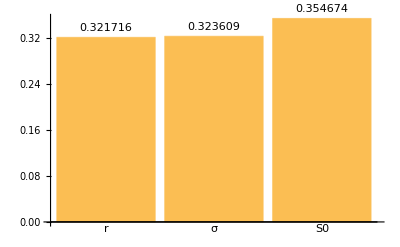

```mathematica
BarChart[Vi/Total[Vi,2],ChartLabels->{"r","σ","S0"},LabelingFunction->Above]
```

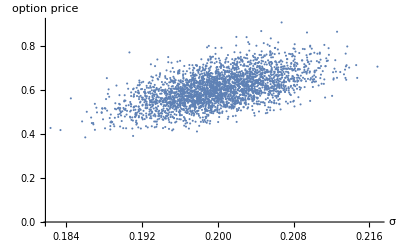

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}]
```

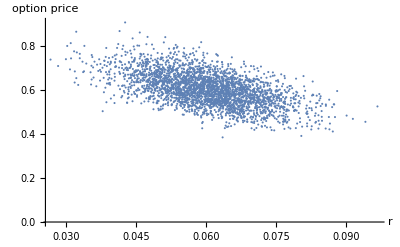

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]
```

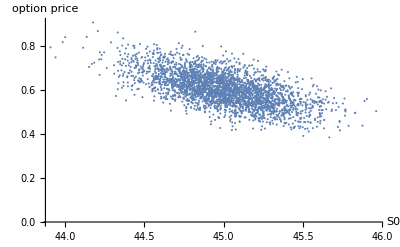

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}]
```

```mathematica
ExportingExtention=15;
```

```mathematica
(*If the variable Exporting was set to True, export the results. This might be useful to avoid repeating lengthy computations.*)
If[Exporting,Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatA"<>ToString[ExportingExtention]<>".m",MatA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatB"<>ToString[ExportingExtention]<>".m",MatB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fA"<>ToString[ExportingExtention]<>".m",fA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fB"<>ToString[ExportingExtention]<>".m",fB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fVA"<>ToString[ExportingExtention]<>".m",fVA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\Param"<>ToString[ExportingExtention]<>".m",Param[[1]]],];
If[Exporting,Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\sigma"<>ToString[ExportingExtention]<>".eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}],"eps"];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\r"<>ToString[ExportingExtention]<>".eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\S0"<>ToString[ExportingExtention]<>".eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}],"eps"],];
```

```mathematica
NotebookSave[]
```

```mathematica
Vars={{0.125,{7.393768280637135*10^(-6),0.00004322870002285361,0.0001161124225516977}},{0.25,{0.00009111790302489225,0.00028003776005258534,0.000692573548432537}},{0.5,{0.0005231448921959867,0.0015428161724180445,0.002867963486243189}},{0.75,{0.001987249189636324,0.0033591847909178133,0.004403610823836773}},{1.0,{0.0022458332820427464,0.0036861312258917676,0.002725724722454316}}};
```